# QNM Curves

Loading the package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["QNMspectral`"]
```

Reproducing the AdS_5 QNM’s of Kovtun, Starinets 0506184

## The equations in EF coordinates

These are the equations of the 5 different modes of the AdS_5-Schwarzschild black brane considered in 0506184 (the modes of the metric, and of an external massless vector field).
The coordinates are such that z=0 is the boundary and z=1 is the horizon. 
For ease of comparison λ=ω/(2π T) and k=q/(2π T).
All equations and functions are rescaled so that the function goes linearly to 0 towards the boundary and the equation itself goes to a nontrivial constant (proportional to the function).

```mathematica
hscalar=(3 (3+4 k^2 z^2+9 z^4)-18 ⅈ z λ) Z3[z]+(3 z (-3+7 z^4)-12 ⅈ z^2 λ) Z3'[z]+3 z^2 (-1+z^4) Z3''[z];
hshear=(12 k^2 (3+4 k^2 z^2-3 z^4) (-1+z^4)+24 ⅈ k^2 z (3+z^4) λ+12 (3+4 k^2 z^2+9 z^4) λ^2-72 ⅈ z λ^3) Z1x[z]+(36 k^2 z (-1+z^4)^2-48 ⅈ k^2 z^2 (-1+z^4) λ+12 z (-3+7 z^4) λ^2-48 ⅈ z^2 λ^3) Z1x'[z]+(12 k^2 z^2 (-1+z^4)^2+12 z^2 (-1+z^4) λ^2) Z1x''[z];
hsound=(4 k^2 (-3+z^4) (3+4 k^2 z^2+z^4)+8 ⅈ k^2 z (9+5 z^4) λ+12 (3+4 k^2 z^2+9 z^4) λ^2-72 ⅈ z λ^3) Z2[z]+(-4 k^2 z (-9+16 z^4+z^8)-16 ⅈ k^2 z^2 (-3+z^4) λ+12 z (-3+7 z^4) λ^2-48 ⅈ z^2 λ^3) Z2'[z]+(4 k^2 z^2 (3-4 z^4+z^8)+12 z^2 (-1+z^4) λ^2) Z2''[z];

Atransverse=(1+4 k^2 z^2+3 z^4-2 ⅈ z λ) Ex[z]+(z (-1+5 z^4)-4 ⅈ z^2 λ) Ex'[z]+z^2 (-1+z^4) Ex''[z];
Adiffusive=(4 k^2 (1+4 k^2 z^2-z^4) (-1+z^4)+8 ⅈ k^2 z (1+3 z^4) λ+4 (1+4 k^2 z^2+3 z^4) λ^2-8 ⅈ z λ^3) Ez[z]+(4 k^2 z (-1+z^4)^2-16 ⅈ k^2 z^2 (-1+z^4) λ+4 z (-1+5 z^4) λ^2-16 ⅈ z^2 λ^3) Ez'[z]+(4 k^2 z^2 (-1+z^4)^2+4 z^2 (-1+z^4) λ^2) Ez''[z];
```

## Computing Modes for the Shear Channel

### Loop Over Complex Momenta

```mathematica
shearModesList = {};
```

```mathematica
ResourceFunction["MonitorProgress"]@Do[
kk = 1 Exp[I θ];
shearMode = GetAccurateModes[hshear/.k->kk,{40,0},{60,0},Eigenfunctions->"Later",Cutoff->6,FilterEigenfunctions->True];
AppendTo[shearModesList,{kk, shearMode[[All,1]]}];
, {θ, 0, 2Pi, 0.1}
]
```

```mathematica
ModesOnCircle[kAbs_, circleStepSize_, minGrid_:50, maxGrid_: 70] := Block[{kk, shearMode, shearModesList, Print},
shearModesList = {};
Do[
kk = kAbs Exp[I θ];
shearMode = GetAccurateModes[hshear/.k->kk,
{minGrid,0},
{maxGrid,0},
Eigenfunctions->"Later",
Cutoff->6,
FilterEigenfunctions->True];
AppendTo[shearModesList,{kk, shearMode[[All,1]]}];
, {θ, 0, 2Pi, circleStepSize}
];
shearModesList
];
```

```mathematica
shearModesListList = {};
```

```mathematica
ResourceFunction["MonitorProgress"]@Do[
shearModesk = ModesOnCircle[kAbs, 0.01];
AppendTo[shearModesListList, {kAbs, shearModesk}];
, {kAbs, 1, 2, 0.1}
];
```

```mathematica
shearModesListListBackup = ; (* iconized version of the result of above calculation *)
```

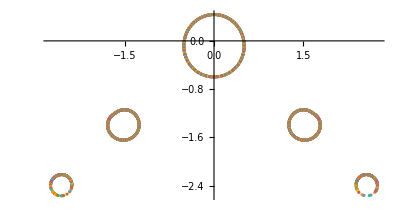

```mathematica
ComplexListPlot[
shearModesListList[[1,2]][[All,2]]
]
```

```mathematica
p1 = Show@Table[
ComplexListPlot[
Transpose@Select[shearModesListList[[i,2]][[All,2]], (Length[#]==5)&],
PlotStyle->{Blue, Orange, Orange, Green, Green},
PlotRange->{{-4,4},{-4,1}}]
, {i, 1, Length@shearModesListList}];
p2 = Show@Table[
ComplexListPlot[
Transpose@Select[shearModesListList[[i,2]][[All,2]], (Length[#]==4)&],
PlotStyle->{Blue, Orange, Orange, Green, Green},
PlotRange->{{-4,4},{-4,1}}]
, {i, 1, Length@shearModesListList}];
```

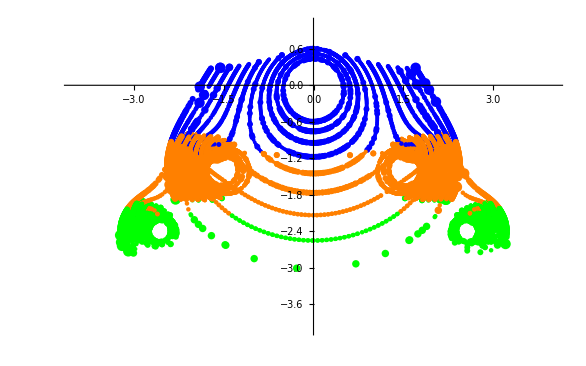

```mathematica
Show[p1,p2]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
individualModes = Flatten[
Table[
Map[CartesianProduct[{#[[1]]}, #[[2]]]&, shearModesListList[[i,2]]]
, {i, 1, Length@shearModesListList}]
, 1];
```

```mathematica
ListPointPlot3D[
Map[{Re[#[[1]]], Im[#[[1]]], Re[#[[2]]]}&, Flatten[individualModes, 1]],
ColorFunction->"Rainbow",
 PlotStyle->PointSize[Medium],
AxesLabel->{"Re q", "Im q", "Re w"}
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[
Map[{Re[#[[1]]], Im[#[[1]]], Im[#[[2]]]}&, Flatten[individualModes, 1]],
ColorFunction->"Rainbow",
 PlotStyle->PointSize[Medium],
AxesLabel->{"Re q", "Im q", "Im w"}
]
```

-Graphics3D-

## New attempt

```mathematica
shearModesListList2Backup = ; (* use this if you don't want to calculate them yourself *)
```

```mathematica
shearModesListList2 = {};
```

```mathematica
ResourceFunction["MonitorProgress"]@Do[
shearModesk = ModesOnCircle[kAbs, 0.03, 80, 100];
AppendTo[shearModesListList2, {kAbs, shearModesk}];
, {kAbs, 1, 1.6, 0.2}
];
```

```mathematica
args = Table[Arg@shearModesListList2[[i,2]][[All, 1]], {i,1,Length@shearModesListList2}];
argsFixed = Table[Table[If[arg >= 0, arg, arg+2 Pi], {arg, args[[i]]}], {i,1,Length@args}];
```

```mathematica
QNMSPlot = Show@Table[
ComplexListPlot[
shearModesListList2[[i,2]][[All,2]],
PlotRange->{{-4,4}, {-3,1.2}},
PlotStyle->ColorData["Rainbow"]/@(argsFixed[[i]]/ (2 Pi))
]
, {i, 1, Length@shearModesListList2}];
BarLegendPlot = ComplexListPlot[
{0,0},
PlotRange->{{-4,4}, {-3,1.1}},
PlotStyle->Opacity[0],
AxesLabel->{"Re w", "Im w"},
PlotLegends->BarLegend[{ColorData["Rainbow"][#/(2 Pi)]&, {0, 2 Pi}}]
]; (* could not figure out a different way of adding this bar legend *)
```

```mathematica
QNMSPlot2 = Show[BarLegendPlot, QNMSPlot]
```

-Graphics-

```mathematica
Export["Figures/QNMsPlot2.pdf", QNMSPlot2]
```

Figures/QNMsPlot2.pdf

```mathematica
individualModes2 = Flatten[
Table[
Map[CartesianProduct[{#[[1]]}, #[[2]]]&, shearModesListList2[[i,2]]]
, {i, 1, Length@shearModesListList2}]
, 1];
```

```mathematica
RiemannSurfRePlot2 = ListPointPlot3D[
Map[{Re[#[[1]]], Im[#[[1]]], Re[#[[2]]]}&, Flatten[individualModes2, 1]],
ColorFunction->"Rainbow",
 PlotStyle->PointSize[Medium],
AxesLabel->{"Re q", "Im q", "Re w"}
]
```

-Graphics3D-

```mathematica
Export["Figures/RiemannSurfRePlot2.pdf", RiemannSurfRePlot2]
```

Figures/RiemannSurfRePlot2.pdf

```mathematica
RiemannSurfImPlot2= ListPointPlot3D[
Map[{Re[#[[1]]], Im[#[[1]]], Im[#[[2]]]}&, Flatten[individualModes2, 1]],
ColorFunction->"Rainbow",
 PlotStyle->PointSize[Medium],
AxesLabel->{"Re q", "Im q", "Im w"}
]
```

-Graphics3D-

```mathematica
Export["Figures/RiemannSurfImPlot2.pdf", RiemannSurfImPlot2]
```

Figures/RiemannSurfImPlot2.pdf

```mathematica
argsFixed[[1, 1;;5]]
```

{0.,0.03,0.06,0.09,0.12}

```mathematica
ii = 1;
```

```mathematica
circleManipulate = Manipulate[
ComplexListPlot[
shearModesListList2[[ii,2]][[1;;iPt,2]],
PlotStyle->ColorData["Rainbow"]/@(argsFixed[[ii, 1;;iPt]]/ (2 Pi)),
PlotRange->{{-4,4}, {-2.5,1.1}},
PlotLabel->"arg(k) = "<>ToString[argsFixed[[ii, iPt]]],
PlotLegends->BarLegend[{ColorData["Rainbow"][#/(2 Pi)]&, {0, 2 Pi}}]
]
, {iPt, 1, Length@shearModesListList2[[ii,2]],1}
]
```

```mathematica
circleMov = Table[
ComplexListPlot[
shearModesListList2[[ii,2]][[iPt;;iPt,2]],
PlotStyle->ColorData["Rainbow"]@(argsFixed[[ii, iPt]]/ (2 Pi)),
PlotRange->{{-4,4}, {-2.5,1.1}},
PlotLabel->"arg(k) = "<>ToString[argsFixed[[ii, iPt]]],
PlotLegends->BarLegend[{ColorData["Rainbow"][#/(2 Pi)]&, {0, 2 Pi}}]
]
, {iPt, 1, Length@shearModesListList2[[ii,2]],1}
];
```

```mathematica
Export["Figures/circleMov.mov", circleManipulate]
```

Figures/circleMov.mov

```mathematica
ListAnimate[circleMov]
```